```mathematica
Úkol 1 
David Papaj
```

Úkol

David Papaj

```mathematica
insertionSort[a_List]:=Module[{A=a},For[i=2,i<=Length[A],i++,value=A[[i]];j=i-1;
While[j>=1&&A[[j]]>value,A[[j+1]]=A[[j]];j--;];
A[[j+1]]=value;];
A]
```

```mathematica
selectSort[x_List]:=Module[{n=1,temp,xi=x,j},While[n<=Length@x,temp=xi[[n]];
For[j=n,j<=Length@x,j++,If[xi[[j]]<temp,temp=xi[[j]]];];
xi[[n;;]]={temp}~Join~Delete[xi[[n;;]],First@Position[xi[[n;;]],temp]];
n++;];
xi]
```

```mathematica
quickSort[x_List]:=Module[{pivot},If[Length@x<=1,Return[x]];
pivot=RandomChoice@x;
Flatten@{quickSort[Cases[x,j_/;j<pivot]],Cases[x,j_/;j==pivot],quickSort[Cases[x,j_/;j>pivot]]}]
```

```mathematica
shellSort[lst_]:=Module[{list=lst,incr,temp,i,j},incr=Round[Length[list]/2];
While[incr>0,For[i=incr+1,i<=Length[list],i++,temp=list[[i]];j=i;
While[(j>=(incr+1))&&(list[[j-incr]]>temp),list[[j]]=list[[j-incr]];j=j-incr;];
list[[j]]=temp;];
If[incr==2,incr=1,incr=Round[incr/2.2]]];list]
```

```mathematica
ClearAll[SortByPos,radixSort]
SortByPos[data:{_List..},pos_Integer]:=Module[{digs,order},digs=data[[All,pos]];
order=Ordering[digs];
data[[order]]]
radixSort[x:{_Integer..}]:=Module[{y,digs,maxlen,offset},offset=Min[x];
y=x-offset;
digs=IntegerDigits/@y;
maxlen=Max[Length/@digs];
digs=IntegerDigits[#,10,maxlen]&/@y;
digs=Fold[SortByPos,digs,-Range[maxlen]];
digs=FromDigits/@digs;
digs+=offset;
digs]
```

```mathematica
strandSort[input_]:=Module[{results={},A=input},While[Length@A>0,sublist={A[[1]]};A=A[[2;;All]];
For[i=1,i<Length@A,i++,If[A[[i]]>Last@sublist,AppendTo[sublist,A[[i]]];A=Delete[A,i];]];
results=#[[Ordering@#]]&@Join[sublist,results];];
results]
```

```mathematica
Attributes[mergeSort]=HoldFirst;

mergeSort[array_Symbol,left_Integer,right_Integer]:=Module[{middle,n1,n2,L,R,i,j,k},
If[left<right,middle=Floor[(left+right)/2];
mergeSort[array,left,middle];
mergeSort[array,middle+1,right];
n1=middle-left+1;
n2=right-middle;
L=ConstantArray[Null,n1];
R=ConstantArray[Null,n2];
For[i=1,i<=n1,++i,L[[i]]=array[[left+i-1]];];
For[j=1,j<=n2,++j,R[[j]]=array[[middle+j]];];
i=1;
j=1;
k=left;
While[i<=n1&&j<=n2,If[L[[i]]<=R[[j]],array[[k]]=L[[i]];
i++;,array[[k]]=R[[j]];
j++;];
k++;];
While[i<=n1,array[[k]]=L[[i]];
i++;
k++;];
While[j<=n2,array[[k]]=R[[j]];
j++;
k++;];
array]]
```

```mathematica
nahodne10=RandomInteger[{0,1000},10]
```

{238,944,223,197,122,885,792,911,497,214}

```mathematica
nahodne100=RandomInteger[{0,1000},100]
```

{115,92,345,744,453,497,287,334,346,44,246,593,954,83,887,291,752,499,765,785,273,292,319,367,722,852,946,293,472,818,974,748,776,180,414,90,476,63,873,266,320,596,902,263,5,728,200,768,88,887,985,807,428,813,115,130,35,984,569,828,807,759,243,44,429,343,518,165,145,619,832,979,563,727,110,847,299,306,540,632,660,849,199,972,643,480,869,67,486,275,432,60,285,263,506,188,244,892,567,962}

```mathematica
nahodne1000=RandomInteger[{0,1000},1000];
```

```mathematica
nahodne10000=RandomInteger[{0,1000},10000];
```

```mathematica
nahodne100000=RandomInteger[{0,1000},100000];
```

```mathematica
vzestupne10=Sort@nahodne10
```

{122,197,214,223,238,497,792,885,911,944}

```mathematica
vzestupne100=Sort@nahodne100
```

{5,35,44,44,60,63,67,83,88,90,92,110,115,115,130,145,165,180,188,199,200,243,244,246,263,263,266,273,275,285,287,291,292,293,299,306,319,320,334,343,345,346,367,414,428,429,432,453,472,476,480,486,497,499,506,518,540,563,567,569,593,596,619,632,643,660,722,727,728,744,748,752,759,765,768,776,785,807,807,813,818,828,832,847,849,852,869,873,887,887,892,902,946,954,962,972,974,979,984,985}

```mathematica
vzestupne1000=Sort@nahodne1000;
```

```mathematica
vzestupne10000=Sort@nahodne10000;
```

```mathematica
vzestupne100000=Sort@nahodne100000;
```

```mathematica
sestupne10=Reverse@vzestupne10
```

{944,911,885,792,497,238,223,214,197,122}

```mathematica
sestupne100=Reverse@vzestupne100
```

{985,984,979,974,972,962,954,946,902,892,887,887,873,869,852,849,847,832,828,818,813,807,807,785,776,768,765,759,752,748,744,728,727,722,660,643,632,619,596,593,569,567,563,540,518,506,499,497,486,480,476,472,453,432,429,428,414,367,346,345,343,334,320,319,306,299,293,292,291,287,285,275,273,266,263,263,246,244,243,200,199,188,180,165,145,130,115,115,110,92,90,88,83,67,63,60,44,44,35,5}

```mathematica
sestupne1000=Reverse@vzestupne1000;
```

```mathematica
sestupne10000=Reverse@vzestupne10000;
```

```mathematica
sestupne100000=Reverse@vzestupne100000;
```

```mathematica
quickSortNahodne10=Mean[Table[AbsoluteTiming[quickSort@nahodne10][[1]],{11}]]
```

0.0003046

```mathematica
quickSortNahodne100=Mean[Table[AbsoluteTiming[quickSort@nahodne100][[1]],{11}]]
```

0.00368936

```mathematica
quickSortNahodne1000=Mean[Table[AbsoluteTiming[quickSort@nahodne1000][[1]],{11}]]
```

0.0292123

```mathematica
quickSortNahodne10000=Mean[Table[AbsoluteTiming[quickSort@nahodne10000][[1]],{11}]]
```

0.166301

```mathematica
quickSortNahodne100000=Mean[Table[AbsoluteTiming[quickSort@nahodne100000][[1]],{11}]]
```

1.24097

```mathematica
shellSortNahodne10=Mean[Table[AbsoluteTiming[shellSort@nahodne10][[1]],{11}]]
```

0.000104236

```mathematica
shellSortNahodne100=Mean[Table[AbsoluteTiming[shellSort@nahodne100][[1]],{11}]]
```

0.00224592

```mathematica
shellSortNahodne1000=Mean[Table[AbsoluteTiming[shellSort@nahodne1000][[1]],{11}]]
```

0.038328

```mathematica
shellSortNahodne10000=Mean[Table[AbsoluteTiming[shellSort@nahodne10000][[1]],{11}]]
```

0.603054

```mathematica
shellSortNahodne100000=Mean[Table[AbsoluteTiming[shellSort@nahodne100000][[1]],{11}]]
```

6.503

```mathematica
radixSortNahodne10=Mean[Table[AbsoluteTiming[radixSort@nahodne10][[1]],{11}]]
```

0.0000583182

```mathematica
radixSortNahodne100=Mean[Table[AbsoluteTiming[radixSort@nahodne100][[1]],{11}]]
```

0.000302427

```mathematica
radixSortNahodne1000=Mean[Table[AbsoluteTiming[radixSort@nahodne1000][[1]],{11}]]
```

0.00137406

```mathematica
radixSortNahodne10000=Mean[Table[AbsoluteTiming[radixSort@nahodne10000][[1]],{11}]]
```

0.0180518

```mathematica
radixSortNahodne100000=Mean[Table[AbsoluteTiming[radixSort@nahodne100000][[1]],{11}]]
```

0.186103

```mathematica
mergeSortNahodne10=Mean[Table[AbsoluteTiming[mergeSort[nahodne10,1,Length[nahodne10]]][[1]],{11}]]
```

0.000863136

```mathematica
mergeSortNahodne100=Mean[Table[AbsoluteTiming[mergeSort[nahodne100,1,Length[nahodne100]]][[1]],{11}]]
```

0.00918325

```mathematica
mergeSortNahodne1000=Mean[Table[AbsoluteTiming[mergeSort[nahodne1000,1,Length[nahodne1000]]][[1]],{11}]]
```

0.0733995

```mathematica
mergeSortNahodne10000=Mean[Table[AbsoluteTiming[mergeSort[nahodne10000,1,Length[nahodne10000]]][[1]],{11}]]
```

0.902653

```mathematica
mergeSortNahodne100000=Mean[Table[AbsoluteTiming[mergeSort[nahodne100000,1,Length[nahodne100000]]][[1]],{11}]]
```

17.4326

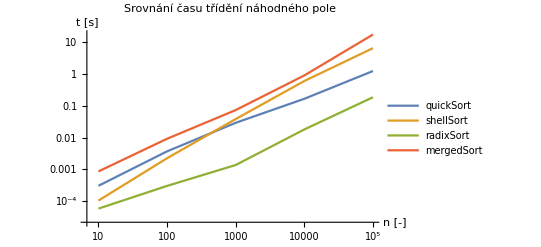

```mathematica
ListLogLogPlot[{
{{10,quickSortNahodne10},{100,quickSortNahodne100},{1000,quickSortNahodne1000},{10000,quickSortNahodne10000},{100000,quickSortNahodne100000}},
{{10,shellSortNahodne10},{100,shellSortNahodne100},{1000,shellSortNahodne1000},{10000,shellSortNahodne10000},{100000,shellSortNahodne100000}},
{{10,radixSortNahodne10},{100,radixSortNahodne100},{1000,radixSortNahodne1000},{10000,radixSortNahodne10000},{100000,radixSortNahodne100000}},
{{10,mergeSortNahodne10},{100,mergeSortNahodne100},{1000,mergeSortNahodne1000},{10000,mergeSortNahodne10000},{100000,mergeSortNahodne100000}}
},
PlotLegends->{"quickSort","shellSort","radixSort","mergedSort"},
Joined->True,
AxesLabel->{"n [-]","t [s]"},
PlotLabel->"Srovnání času třídění náhodného pole"
]
```

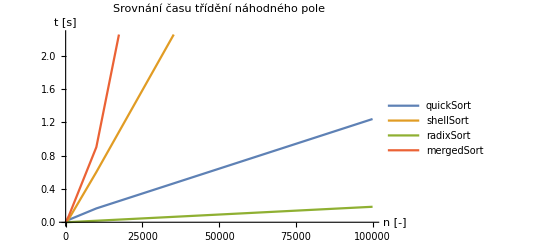

```mathematica
ListPlot[{
{{10,quickSortNahodne10},{100,quickSortNahodne100},{1000,quickSortNahodne1000},{10000,quickSortNahodne10000},{100000,quickSortNahodne100000}},
{{10,shellSortNahodne10},{100,shellSortNahodne100},{1000,shellSortNahodne1000},{10000,shellSortNahodne10000},{100000,shellSortNahodne100000}},
{{10,radixSortNahodne10},{100,radixSortNahodne100},{1000,radixSortNahodne1000},{10000,radixSortNahodne10000},{100000,radixSortNahodne100000}},
{{10,mergeSortNahodne10},{100,mergeSortNahodne100},{1000,mergeSortNahodne1000},{10000,mergeSortNahodne10000},{100000,mergeSortNahodne100000}}
},
PlotLegends->{"quickSort","shellSort","radixSort","mergedSort"},
Joined->True,
AxesLabel->{"n [-]","t [s]"},
PlotLabel->"Srovnání času třídění náhodného pole"
]
```

```mathematica
Grid[{
{"Srovnání času třídění náhodného pole",SpanFromLeft},
{"n","QuickSort","ShellSort","RadixSort","MergeSort"},
{10,quickSortNahodne10,shellSortNahodne10,radixSortNahodne10,mergeSortNahodne10},
{100,quickSortNahodne100,shellSortNahodne100,radixSortNahodne100,mergeSortNahodne100},
{1000,quickSortNahodne1000,shellSortNahodne1000,radixSortNahodne1000,mergeSortNahodne1000},
{10000,quickSortNahodne10000,shellSortNahodne10000,radixSortNahodne10000,mergeSortNahodne10000},
{100000,quickSortNahodne100000,shellSortNahodne100000,radixSortNahodne100000,mergeSortNahodne100000}
},
Dividers->{False,{False,Thick,True,{False},Thick}}
]
```

Srovnání času třídění náhodného pole |  |  |  | 
n | QuickSort | ShellSort | RadixSort | MergeSort
10 | 0.0003046 | 0.000104236 | 0.0000583182 | 0.000863136
100 | 0.00368936 | 0.00224592 | 0.000302427 | 0.00918325
1000 | 0.0292123 | 0.038328 | 0.00137406 | 0.0733995
10000 | 0.166301 | 0.603054 | 0.0180518 | 0.902653
100000 | 1.24097 | 6.503 | 0.186103 | 17.4326

```mathematica
quickSortVzestupne10=Mean[Table[AbsoluteTiming[quickSort@vzestupne10][[1]],{11}]]
```

0.000188345

```mathematica
quickSortVzestupne100=Mean[Table[AbsoluteTiming[quickSort@vzestupne100][[1]],{11}]]
```

0.00197673

```mathematica
quickSortVzestupne1000=Mean[Table[AbsoluteTiming[quickSort@vzestupne1000][[1]],{11}]]
```

0.0195429

```mathematica
quickSortVzestupne10000=Mean[Table[AbsoluteTiming[quickSort@vzestupne10000][[1]],{11}]]
```

0.147307

```mathematica
quickSortVzestupne100000=Mean[Table[AbsoluteTiming[quickSort@vzestupne100000][[1]],{11}]]
```

1.20132

```mathematica
shellSortVzestupne10=Mean[Table[AbsoluteTiming[shellSort@vzestupne10][[1]],{11}]]
```

0.0000956818

```mathematica
shellSortVzestupne100=Mean[Table[AbsoluteTiming[shellSort@vzestupne100][[1]],{11}]]
```

0.00152836

```mathematica
shellSortVzestupne1000=Mean[Table[AbsoluteTiming[shellSort@vzestupne1000][[1]],{11}]]
```

0.0248052

```mathematica
shellSortVzestupne10000=Mean[Table[AbsoluteTiming[shellSort@vzestupne10000][[1]],{11}]]
```

0.374792

```mathematica
shellSortVzestupne100000=Mean[Table[AbsoluteTiming[shellSort@vzestupne100000][[1]],{11}]]
```

4.1924

```mathematica
radixSortVzestupne10=Mean[Table[AbsoluteTiming[radixSort@vzestupne10][[1]],{11}]]
```

0.0000506182

```mathematica
radixSortVzestupne100=Mean[Table[AbsoluteTiming[radixSort@vzestupne100][[1]],{11}]]
```

0.000349018

```mathematica
radixSortVzestupne1000=Mean[Table[AbsoluteTiming[radixSort@vzestupne1000][[1]],{11}]]
```

0.00130693

```mathematica
radixSortVzestupne10000=Mean[Table[AbsoluteTiming[radixSort@vzestupne10000][[1]],{11}]]
```

0.0149001

```mathematica
radixSortVzestupne100000=Mean[Table[AbsoluteTiming[radixSort@vzestupne100000][[1]],{11}]]
```

0.165777

```mathematica
mergeSortVzestupne10=Mean[Table[AbsoluteTiming[mergeSort[vzestupne10,1,Length[vzestupne10]]][[1]],{11}]]
```

0.000581427

```mathematica
mergeSortVzestupne100=Mean[Table[AbsoluteTiming[mergeSort[vzestupne100,1,Length[vzestupne100]]][[1]],{11}]]
```

0.00717125

```mathematica
mergeSortVzestupne1000=Mean[Table[AbsoluteTiming[mergeSort[vzestupne1000,1,Length[vzestupne1000]]][[1]],{11}]]
```

0.0749945

```mathematica
mergeSortVzestupne10000=Mean[Table[AbsoluteTiming[mergeSort[vzestupne100000,1,Length[vzestupne100000]]][[1]],{11}]]
```

16.9374

```mathematica
mergeSortVzestupne100000=Mean[Table[AbsoluteTiming[mergeSort[vzestupne100000,1,Length[vzestupne100000]]][[1]],{11}]]
```

17.1243

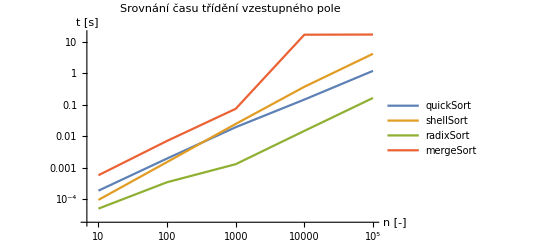

```mathematica
ListLogLogPlot[{
{{10,quickSortVzestupne10},{100,quickSortVzestupne100},{1000,quickSortVzestupne1000},{10000,quickSortVzestupne10000},{100000,quickSortVzestupne100000}},
{{10,shellSortVzestupne10},{100,shellSortVzestupne100},{1000,shellSortVzestupne1000},{10000,shellSortVzestupne10000},{100000,shellSortVzestupne100000}},
{{10,radixSortVzestupne10},{100,radixSortVzestupne100},{1000,radixSortVzestupne1000},{10000,radixSortVzestupne10000},{100000,radixSortVzestupne100000}},
{{10,mergeSortVzestupne10},{100,mergeSortVzestupne100},{1000,mergeSortVzestupne1000},{10000,mergeSortVzestupne10000},{100000,mergeSortVzestupne100000}}
},
PlotLegends->{"quickSort","shellSort","radixSort","mergeSort"},
Joined->True,
AxesLabel->{"n [-]","t [s]"},
PlotLabel->"Srovnání času třídění vzestupného pole"
]
```

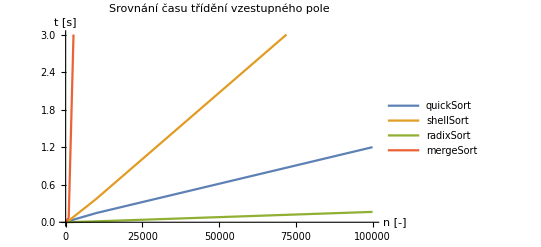

```mathematica
ListPlot[{
{{10,quickSortVzestupne10},{100,quickSortVzestupne100},{1000,quickSortVzestupne1000},{10000,quickSortVzestupne10000},{100000,quickSortVzestupne100000}},
{{10,shellSortVzestupne10},{100,shellSortVzestupne100},{1000,shellSortVzestupne1000},{10000,shellSortVzestupne10000},{100000,shellSortVzestupne100000}},
{{10,radixSortVzestupne10},{100,radixSortVzestupne100},{1000,radixSortVzestupne1000},{10000,radixSortVzestupne10000},{100000,radixSortVzestupne100000}},
{{10,mergeSortVzestupne10},{100,mergeSortVzestupne100},{1000,mergeSortVzestupne1000},{10000,mergeSortVzestupne10000},{100000,mergeSortVzestupne100000}}
},
PlotLegends->{"quickSort","shellSort","radixSort","mergeSort"},
Joined->True,
AxesLabel->{"n [-]","t [s]"},
PlotLabel->"Srovnání času třídění vzestupného pole"
]
```

```mathematica
Grid[{
{"Srovnání času třídění vzestupného pole",SpanFromLeft},
{"n","QuickSort","ShellSort","RadixSort","MergeSort"},
{10,quickSortVzestupne10,shellSortVzestupne10,radixSortVzestupne10,mergeSortVzestupne10},
{100,quickSortVzestupne100,shellSortVzestupne100,radixSortVzestupne100,mergeSortVzestupne100},
{1000,quickSortVzestupne1000,shellSortVzestupne1000,radixSortVzestupne1000,mergeSortVzestupne1000},
{10000,quickSortVzestupne10000,shellSortVzestupne10000,radixSortVzestupne10000,mergeSortVzestupne10000},
{100000,quickSortVzestupne100000,shellSortVzestupne100000,radixSortVzestupne100000,mergeSortVzestupne100000}
},
Dividers->{False,{False,Thick,True,{False},Thick}}
]
```

Srovnání času třídění vzestupného pole |  |  |  | 
n | QuickSort | ShellSort | RadixSort | MergeSort
10 | 0.000188345 | 0.0000956818 | 0.0000506182 | 0.000581427
100 | 0.00197673 | 0.00152836 | 0.000349018 | 0.00717125
1000 | 0.0195429 | 0.0248052 | 0.00130693 | 0.0749945
10000 | 0.147307 | 0.374792 | 0.0149001 | 16.9374
100000 | 1.20132 | 4.1924 | 0.165777 | 17.1243

```mathematica
quickSortSestupne10=Mean[Table[AbsoluteTiming[quickSort@sestupne10][[1]],{11}]]
```

0.000190873

```mathematica
quickSortSestupne100=Mean[Table[AbsoluteTiming[quickSort@sestupne100][[1]],{11}]]
```

0.00201047

```mathematica
quickSortSestupne1000=Mean[Table[AbsoluteTiming[quickSort@sestupne1000][[1]],{11}]]
```

0.0196417

```mathematica
quickSortSestupne10000=Mean[Table[AbsoluteTiming[quickSort@sestupne10000][[1]],{11}]]
```

0.144375

```mathematica
quickSortSestupne100000=Mean[Table[AbsoluteTiming[quickSort@sestupne100000][[1]],{11}]]
```

1.24702

```mathematica
shellSortSestupne10=Mean[Table[AbsoluteTiming[shellSort@sestupne10][[1]],{11}]]
```

0.000127209

```mathematica
shellSortSestupne100=Mean[Table[AbsoluteTiming[shellSort@sestupne100][[1]],{11}]]
```

0.00199969

```mathematica
shellSortSestupne1000=Mean[Table[AbsoluteTiming[shellSort@sestupne1000][[1]],{11}]]
```

0.0283017

```mathematica
shellSortSestupne10000=Mean[Table[AbsoluteTiming[shellSort@sestupne10000][[1]],{11}]]
```

0.435324

```mathematica
shellSortSestupne100000=Mean[Table[AbsoluteTiming[shellSort@sestupne100000][[1]],{11}]]
```

4.91951

```mathematica
radixSortSestupne10=Mean[Table[AbsoluteTiming[radixSort@sestupne10][[1]],{11}]]
```

0.0000505455

```mathematica
radixSortSestupne100=Mean[Table[AbsoluteTiming[radixSort@sestupne100][[1]],{11}]]
```

0.0002775

```mathematica
radixSortSestupne1000=Mean[Table[AbsoluteTiming[radixSort@sestupne1000][[1]],{11}]]
```

0.00133673

```mathematica
radixSortSestupne10000=Mean[Table[AbsoluteTiming[radixSort@sestupne10000][[1]],{11}]]
```

0.0146445

```mathematica
radixSortSestupne100000=Mean[Table[AbsoluteTiming[radixSort@sestupne100000][[1]],{11}]]
```

0.145631

```mathematica
mergeSortSestupne10=Mean[Table[AbsoluteTiming[mergeSort[sestupne10,1,Length[sestupne10]]][[1]],{11}]]
```

0.000829327

```mathematica
mergeSortSestupne100=Mean[Table[AbsoluteTiming[mergeSort[sestupne100,1,Length[sestupne100]]][[1]],{11}]]
```

0.00678311

```mathematica
mergeSortSestupne1000=Mean[Table[AbsoluteTiming[mergeSort[sestupne1000,1,Length[sestupne1000]]][[1]],{11}]]
```

0.0725683

```mathematica
mergeSortSestupne10000=Mean[Table[AbsoluteTiming[mergeSort[sestupne10000,1,Length[sestupne10000]]][[1]],{11}]]
```

0.865035

```mathematica
mergeSortSestupne100000=Mean[Table[AbsoluteTiming[mergeSort[sestupne100000,1,Length[sestupne100000]]][[1]],{11}]]
```

16.9544

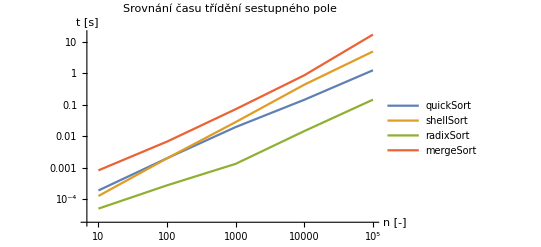

```mathematica
ListLogLogPlot[{
{{10,quickSortSestupne10},{100,quickSortSestupne100},{1000,quickSortSestupne1000},{10000,quickSortSestupne10000},{100000,quickSortSestupne100000}},
{{10,shellSortSestupne10},{100,shellSortSestupne100},{1000,shellSortSestupne1000},{10000,shellSortSestupne10000},{100000,shellSortSestupne100000}},
{{10,radixSortSestupne10},{100,radixSortSestupne100},{1000,radixSortSestupne1000},{10000,radixSortSestupne10000},{100000,radixSortSestupne100000}},
{{10,mergeSortSestupne10},{100,mergeSortSestupne100},{1000,mergeSortSestupne1000},{10000,mergeSortSestupne10000},{100000,mergeSortSestupne100000}}
},
PlotLegends->{"quickSort","shellSort","radixSort","mergeSort"},
Joined->True,
AxesLabel->{"n [-]","t [s]"},
PlotLabel->"Srovnání času třídění sestupného pole"
]
```

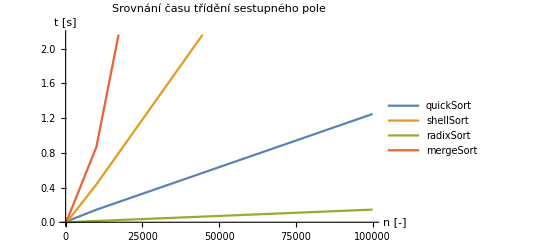

```mathematica
ListPlot[{
{{10,quickSortSestupne10},{100,quickSortSestupne100},{1000,quickSortSestupne1000},{10000,quickSortSestupne10000},{100000,quickSortSestupne100000}},
{{10,shellSortSestupne10},{100,shellSortSestupne100},{1000,shellSortSestupne1000},{10000,shellSortSestupne10000},{100000,shellSortSestupne100000}},
{{10,radixSortSestupne10},{100,radixSortSestupne100},{1000,radixSortSestupne1000},{10000,radixSortSestupne10000},{100000,radixSortSestupne100000}},
{{10,mergeSortSestupne10},{100,mergeSortSestupne100},{1000,mergeSortSestupne1000},{10000,mergeSortSestupne10000},{100000,mergeSortSestupne100000}}
},
PlotLegends->{"quickSort","shellSort","radixSort","mergeSort"},
Joined->True,
AxesLabel->{"n [-]","t [s]"},
PlotLabel->"Srovnání času třídění sestupného pole"
]
```

```mathematica
Grid[{
{"Srovnání času třídění sestupného pole",SpanFromLeft},
{"n","QuickSort","ShellSort","RadixSort","MergeSort"},
{10,quickSortSestupne10,shellSortSestupne10,radixSortSestupne10,mergeSortSestupne10},
{100,quickSortSestupne100,shellSortSestupne100,radixSortSestupne100,mergeSortSestupne100},
{1000,quickSortSestupne1000,shellSortSestupne1000,radixSortSestupne1000,mergeSortSestupne1000},
{10000,quickSortSestupne10000,shellSortSestupne10000,radixSortSestupne10000,mergeSortSestupne10000},
{100000,quickSortSestupne100000,shellSortSestupne100000,radixSortSestupne100000,mergeSortSestupne100000}
},
Dividers->{False,{False,Thick,True,{False},Thick}}
]
```

Srovnání času třídění sestupného pole |  |  |  | 
n | QuickSort | ShellSort | RadixSort | MergeSort
10 | 0.000190873 | 0.000127209 | 0.0000505455 | 0.000829327
100 | 0.00201047 | 0.00199969 | 0.0002775 | 0.00678311
1000 | 0.0196417 | 0.0283017 | 0.00133673 | 0.0725683
10000 | 0.144375 | 0.435324 | 0.0146445 | 0.865035
100000 | 1.24702 | 4.91951 | 0.145631 | 16.9544

```mathematica
Závěr
```

Závěr

Nejrychlejší v těchto výpočtech  byl pokaždé RadixSort a nejhorší byl algoritmus MergeSort, ale pořád lepší o mnoho rychlější než InsertSort,SelectSort,BubbleSort a StrandSort u kterých v sestupném poli o  hodnotě 100 000  byly tyto algoritmy zcela nepoužitelné oproti jiným algoritmům(časově) .
Také  výhoda je hlavně jak jednoduché a kratké jsou. Hodí se především na třídění menších množství dat.

U zdůvodu časové obtížnosti u algoritmů O(n2) jsem je nemohl dokončit, protože výpočet třídění sestupného pole by trvalo 2hod každý cyklus, takže +-22hod a proto jsem poslední algoritmus vyměnil za mnoho rychlejší MergeSort.

O(n2) je nejpomalější algoritmus,ale zato jeho výhoda je jeho jednoduchost.U složitosti O(n2) se doba trvání průběhu zvyšuje kvadraticky, tedy pokud se zvýší délka vstupu dvakrát, potřebný čas se zvýší čtyřikrát.
O(N^2) je pro → 2 vnořené „cykly for“, pokud jsou 3 vnořené smyčky for, bude pak časová složitost O(N^3).

```mathematica
Test
```

Test

```mathematica
random=RandomInteger[{0,1000},100]
```

{142,847,909,871,988,857,5,525,873,289,522,278,631,221,891,226,238,689,522,775,696,435,48,460,725,865,521,926,623,999,379,708,990,368,170,618,872,577,184,94,833,825,30,222,470,649,493,764,423,341,366,646,247,990,539,155,629,826,426,449,951,617,962,792,342,118,447,871,760,758,74,130,483,168,710,878,426,506,60,639,787,183,202,567,761,744,3,122,961,400,101,845,33,368,457,634,174,827,547,834}

```mathematica
insertionSort@random
```

{3,5,30,33,48,60,74,94,101,118,122,130,142,155,168,170,174,183,184,202,221,222,226,238,247,278,289,341,342,366,368,368,379,400,423,426,426,435,447,449,457,460,470,483,493,506,521,522,522,525,539,547,567,577,617,618,623,629,631,634,639,646,649,689,696,708,710,725,744,758,760,761,764,775,787,792,825,826,827,833,834,845,847,857,865,871,871,872,873,878,891,909,926,951,961,962,988,990,990,999}

```mathematica
selectSort@random
```

{3,5,30,33,48,60,74,94,101,118,122,130,142,155,168,170,174,183,184,202,221,222,226,238,247,278,289,341,342,366,368,368,379,400,423,426,426,435,447,449,457,460,470,483,493,506,521,522,522,525,539,547,567,577,617,618,623,629,631,634,639,646,649,689,696,708,710,725,744,758,760,761,764,775,787,792,825,826,827,833,834,845,847,857,865,871,871,872,873,878,891,909,926,951,961,962,988,990,990,999}

```mathematica
quickSort@random
```

{3,5,30,33,48,60,74,94,101,118,122,130,142,155,168,170,174,183,184,202,221,222,226,238,247,278,289,341,342,366,368,368,379,400,423,426,426,435,447,449,457,460,470,483,493,506,521,522,522,525,539,547,567,577,617,618,623,629,631,634,639,646,649,689,696,708,710,725,744,758,760,761,764,775,787,792,825,826,827,833,834,845,847,857,865,871,871,872,873,878,891,909,926,951,961,962,988,990,990,999}

```mathematica
shellSort@random
```

{3,5,30,33,48,60,74,94,101,118,122,130,142,155,168,170,174,183,184,202,221,222,226,238,247,278,289,341,342,366,368,368,379,400,423,426,426,435,447,449,457,460,470,483,493,506,521,522,522,525,539,547,567,577,617,618,623,629,631,634,639,646,649,689,696,708,710,725,744,758,760,761,764,775,787,792,825,826,827,833,834,845,847,857,865,871,871,872,873,878,891,909,926,951,961,962,988,990,990,999}

```mathematica
radixSort@random
```

{3,5,30,33,48,60,74,94,101,118,122,130,142,155,168,170,174,183,184,202,221,222,226,238,247,278,289,341,342,366,368,368,379,400,423,426,426,435,447,449,457,460,470,483,493,506,521,522,522,525,539,547,567,577,617,618,623,629,631,634,639,646,649,689,696,708,710,725,744,758,760,761,764,775,787,792,825,826,827,833,834,845,847,857,865,871,871,872,873,878,891,909,926,951,961,962,988,990,990,999}

```mathematica
strandSort@random
```

{3,5,30,33,48,60,74,94,101,118,122,130,142,155,168,170,174,183,184,202,221,222,226,238,247,278,289,341,342,366,368,368,379,400,423,426,426,435,447,449,457,460,470,483,493,506,521,522,522,525,539,547,567,577,617,618,623,629,631,634,639,646,649,689,696,708,710,725,744,758,760,761,764,775,787,792,825,826,827,833,834,845,847,857,865,871,871,872,873,878,891,909,926,951,961,962,988,990,990,999}

```mathematica
mergeSort[random,1,Length[random]]
```

{3,5,30,33,48,60,74,94,101,118,122,130,142,155,168,170,174,183,184,202,221,222,226,238,247,278,289,341,342,366,368,368,379,400,423,426,426,435,447,449,457,460,470,483,493,506,521,522,522,525,539,547,567,577,617,618,623,629,631,634,639,646,649,689,696,708,710,725,744,758,760,761,764,775,787,792,825,826,827,833,834,845,847,857,865,871,871,872,873,878,891,909,926,951,961,962,988,990,990,999}